Experimenting with Raw Audio Data - Testing Functions

```mathematica
audioRawData = Import["/Users/shubhamkumar/Downloads/prenks/Summer Bummer Demo - LDR.mp3"]
```

```mathematica
Spectrogram[audioRawData]
```

-Graphics-

```mathematica
trimmedRawData = AudioTrim[audioRawData, {0,30}]
```

```mathematica
stereoTrimmedRawData = AudioChannelMix[trimmedAudioRawData, "Mono"]
```

1

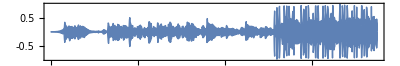

```mathematica
AudioChannels[stereoTrimmedRawData]
AudioPlot[stereoTrimmedRawData]
```

```mathematica
Audio[stereoTrimmedRawData, AudioChannelAssignment->{1}]
```

```mathematica
test = AudioGenerator["Sin", 10]
```

```mathematica
AudioChannels[test]
```

1

```mathematica
chanelledTest =Audio[test, AudioChannelAssignment->{2}]
```

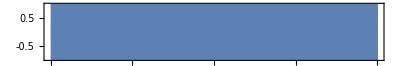

-Graphics-

```mathematica
AudioPlot[test]
AudioPlot[chanelledTest]
```

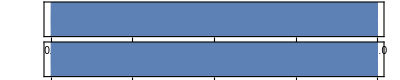

```mathematica
AudioPlot[AudioChannelMix[test, "Stereo"]]
```

```mathematica
a = Audio[AudioChannelMix[ExampleData[{"Audio", "FemaleVoice"}, "Audio"], "Mono"], AudioChannelAssignment -> {2}];
(*b=Audio[ExampleData[{"Audio","MaleVoice"},"Audio"], AudioChannelAssignment->{1}];*)
Export[ "/Users/shubhamkumar/Desktop/prenk.mp3",a]
```

/Users/shubhamkumar/Desktop/prenk.mp3

```mathematica
AudioChannelCombine[{a,b}]
```

```mathematica
AudioChannels/@{a,b}
```

{2,2}

```mathematica
AudioPartition
```